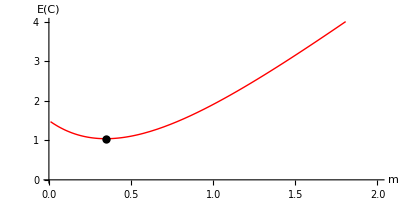

```mathematica
Plot[{3/2(2m+2 ⅇ^(-2m)-1)},{m,0.01,2},AspectRatio->0.5,AxesLabel->{m,"E(C)"},Epilog->{PointSize[0.015],Point[{Log[√2],3Log[√2]}]},PlotRange->{0,4},GridLines->{{Log[√2]},{3Log[√2]}} ,PlotStyle->{Directive[Red,Thick]}]
```

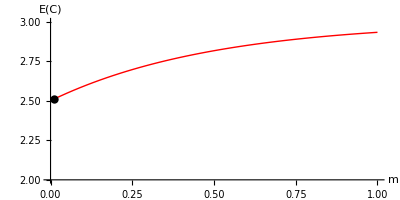

```mathematica
Plot[{3-1/2 ⅇ^(-2m)},{m,0.01,1},AspectRatio->.5,AxesLabel->{m,"E(C)"},AxesOrigin->{0,2},Epilog->{PointSize[0.015],Point[{0.01,3-1/2 ⅇ^(-2/100)}]},PlotRange->{2,3},GridLines->{{0.01},{3-1/2 ⅇ^(-2/100)}} ,PlotStyle->{Directive[Red,Thick]}]
```

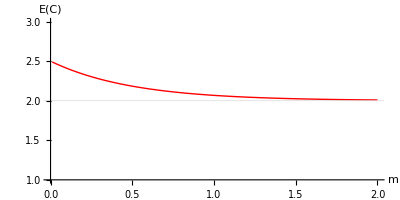

```mathematica
Plot[{2+1/2 ⅇ^(-2m)},{m,0.01,2},AspectRatio->.5,AxesLabel->{m,"E(C)"},AxesOrigin->{0,1},PlotRange->{1,3},GridLines->{{},{2}},PerformanceGoal->"Quality",PlotStyle->{Directive[Red,Thick]}]
```

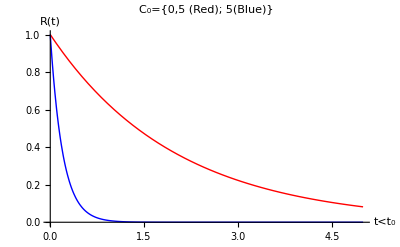

```mathematica
Plot[Evaluate[Table[ⅇ^-(1/2(9n-8)  t),{n,1,2}]],{t,0,5},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick],Directive[Green,Thick],Yellow,Orange},PlotRange->{0,1}, AxesLabel->{t<Subscript[t, 0],"R(t)"},PlotLabel->"C_0={0,5 (Red); 5(Blue)}",PerformanceGoal->"Quality"]
```

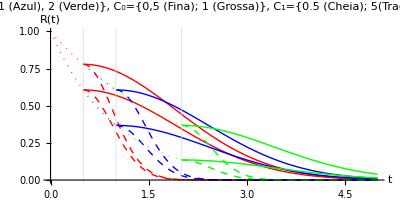

```mathematica
Show[
Plot[0,{t,0,5},PlotStyle->{Opacity[0]}, PlotRange->{0,1},AxesLabel->{t,"R(t)"},GridLines->{{.5,1,2},{2}},PerformanceGoal->"Quality",AspectRatio->.5,PlotPoints->100, PlotLabel->"t_0={0.5 (Vermelho), 1 (Azul), 2 (Verde)},
C_0={0,5 (Fina); 1 (Grossa)}, 
C_1={0.5 (Cheia); 5(Tracejada)}, 
t<t_0(Pontilhada)"],
Plot[{ⅇ^-((.5) (.5)+1/2 (.5)(t-(.5))^2),ⅇ^-((.5)( .5)+1/2(5)(t-(.5))^2),ⅇ^-((1)(.5)+1/2( .5)(t-(.5))^2),ⅇ^-((1)(.5)+1/2 (5)(t-(.5))^2)},{t,.5,5},PlotPoints->200, PlotStyle->{Directive[Red,Thin],Directive[Red,Thin,Dashed],Directive[Red,Thick],Directive[Red, Thick, Dashed]}],
Plot[{ⅇ^-(.5 t),ⅇ^-(1 t)},{t,0,.5},PlotPoints->200, PlotStyle->{Directive[Red,Thin,Dotted],Directive[Red,Thick,Dotted]}],

Plot[{ⅇ^-((.5) (1)+1/2 (.5)(t-(1))^2),ⅇ^-((.5) (1)+1/2 (5)(t-(1))^2),ⅇ^-((1) (1)+1/2 (.5)(t-(1))^2),ⅇ^-((1)(1)+1/2 (5)(t-(1))^2)},{t,1,5},PlotPoints->200,
PlotStyle->{Directive[Blue, Thin],Directive[Blue, Thin,Dashed],Directive[Blue,Thick],Directive[Blue, Thick, Dashed]}],Plot[{ⅇ^-(.5 t),ⅇ^-(1 t)},{t,.5,1},PlotPoints->200, PlotStyle->{Directive[Blue,Thin,Dotted],Directive[Blue,Thick,Dotted]}],

Plot[{ⅇ^-((.5) (2)+1/2 (.5)(t-(2))^2),ⅇ^-((.5) (2)+1/2 (5)(t-(2))^2),ⅇ^-((1) (2)+1/2 (.5)(t-(2))^2),ⅇ^-(1 2+1/2 5(t-2)^2)},{t,2,5},PlotPoints->200,
PlotStyle->{Directive[Green, Thin],Directive[Green, Thin, Dashed],Directive[Green, Thick],Directive[Green, Thick, Dashed]}],Plot[{ⅇ^-(.5 t),ⅇ^-(1 t)},{t,1,2},PlotPoints->200, PlotStyle->{Directive[Green,Thin,Dotted],Directive[Green,Thick,Dotted]}]
]
```

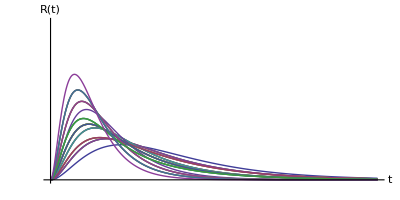

```mathematica
Plot[Evaluate[Table[a ⅇ^-(a t)+b ⅇ^-(b t)+c ⅇ^-(c t)-(a+b)ⅇ^-((a+b )t)-(a+c)ⅇ^-((a+c )t)-(b+c)ⅇ^-((b+c )t)+(a+b+c)ⅇ^-((a+b+c )t),{a,1,3},{b,1,3},{c,1,3}]],{t,0,5},PlotPoints->200,PlotRange->{0,2},AxesLabel->{t,"R(t)"},AspectRatio->.5, Ticks->None]
```